```mathematica
threadData
```

Dataset[<>]

```mathematica
dataByDescription=threadData[GroupBy["dataDescription"]]
```

Dataset[<>]

```mathematica
(*---------------------------- SH  DATA ----------------------------*)
```

```mathematica
shData=dataByDescription[[1]];
```

```mathematica
shData[Select[#Date=="10/9/18"&]];
```

```mathematica
DateObject[shData[[1]][[3]]]
```

DateObject::ambig: Warning: the interpretation of the string 10/9/18 8:28:00 as a date is ambiguous.

Tue 9 Oct 2018 08:28:00GMT-7.

```mathematica
(*-----Tuesday------*)
```

```mathematica
shDataTuesday=shData[Select[#Date=="10/9/18"&]];
```

```mathematica
(*-----Wednesday-----*)
```

```mathematica
shDataWednesday=shData[Select[#Date=="10/10/18"&]];
```

```mathematica
(*-----Thursday-----*)
```

```mathematica
shDataThursday=shData[Select[#Date=="10/11/18"&]];
```

```mathematica
(*----------------------------- FU  DATA --------------------------*)
```

```mathematica
fuData=dataByDescription[[2]];
```

```mathematica
fuData[Select[#Date=="10/9/18"&]];
(*-----Tuesday-----*)
```

```mathematica
fuDataTuesday=fuData[Select[#Date=="10/9/18"&]];
(*-----Wednesday-----*)
fuDataWednesday=fuData[Select[#Date=="10/10/18"&]];
```

```mathematica
(*-----Thursday-----*)
fuDataThursday=fuData[Select[#Date=="10/11/18"&]];
```

```mathematica
(*----------------------------- PIS OFF  DATA ----------------------------*)
```

```mathematica
pisOffData=dataByDescription[[3]];
pisOffData[Select[#Date=="10/9/18"&]];
```

```mathematica
(*-----Tuesday-----*)
pisOffDataTuesday=pisOffData[Select[#Date=="10/9/18"&]];
```

```mathematica
(*-----Wednesday-----*)
pisOffDataWednesday=pisOffData[Select[#Date=="10/10/18"&]];
(*-----Thursday-----*)
pisOffDataThursday=pisOffData[Select[#Date=="10/11/18"&]];



(*----------------------------- GD DAM  DATA ----------------------------------*)
```

```mathematica
gdDamData=dataByDescription[[4]];
gdDamData[Select[#Date=="10/9/18"&]];

(*-----Tuesday-----*)
gdDamDataTuesday=gdDamData[Select[#Date=="10/9/18"&]];
(*-----Wednesday-----*)
gdDamDataWednesday=gdDamData[Select[#Date=="10/10/18"&]];
(*-----Thursday-----*)
gdDamDataThursday=gdDamData[Select[#Date=="10/11/18"&]];



(*---------------------------------- BI  DATA -----------------------------------*)
```

```mathematica
biData=dataByDescription[[5]];
biData[Select[#Date=="10/9/18"&]];
```

```mathematica
(*-----Tuesday-----*)
biDataTuesday=biData[Select[#Date=="10/9/18"&]];
```

```mathematica
(*-----Wednesday-----*)
biDataWednesday=biData[Select[#Date=="10/10/18"&]];
```

```mathematica
(*-----Thursday-----*)
biDataThursday=biData[Select[#Date=="10/11/18"&]];



(*------------------------------------ AS  DATA ----------------------------------*)
```

```mathematica
asData=dataByDescription[[6]];
asData[Select[#Date"10/9/18"&]];

(*-----Tuesday-----*)
asDataTuesday=asData[Select[#Date=="10/9/18"&]];
```

```mathematica
(*-----Wednesday-----*)
```

```mathematica
asDataWednesday=asData[Select[#Date=="10/10/18"&]];
(*-----Thursday-----*)
asDataThursday=asData[Select[#Date=="10/11/18"&]];
```

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
FINALDATES={shDataTuesday,shDataWednesday}
```

{Dataset[<>],Dataset[<>]}

DateObject::ambig: Warning: the interpretation of the string 10/9/18 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 10/9/18 8:28:00 as a date is ambiguous.

DateObject::ambig: Warning: the interpretation of the string 10/9/18 as a date is ambiguous.

General::stop: Further output of DateObject::ambig will be suppressed during this calculation.

DateHistogram::hbins: The bin specification Dataset[«2»] cannot be used to determine either how many or which bins to use.

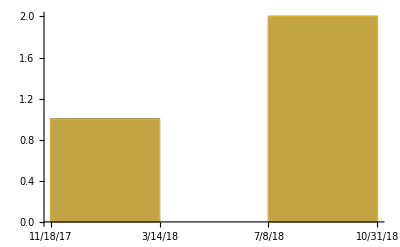

```mathematica
DateHistogram[shDataTuesday,shDataWednesday]
```